Graph Theory

## j00 h4>< ?

```mathematica
WordData["hacker"]// TableForm
```

hacker | Noun | UnskilledPerson
hacker | Noun | Coder
hacker | Noun | GolfPlayer
hacker | Noun | Terrorist

```mathematica
WordData["hacker","Definitions"]//TableForm
```

{hacker,Noun,UnskilledPerson}→one who works hard at boring tasks
{hacker,Noun,Coder}→a programmer for whom computing is its own reward; may enjoy the challenge of breaking into other computers but does no harm
{hacker,Noun,GolfPlayer}→someone who plays golf poorly
{hacker,Noun,Terrorist}→a programmer who breaks into computer systems in order to steal or change or destroy information as a form of cyber-terrorism

```mathematica
words=DictionaryLookup["hack*"];
Flatten[Map[(Thread[#->DeleteCases[Nearest[words,#,3],#]])&,words]];
Graph[%,VertexLabels->"Name",ImagePadding->20,ImageSize->450]
```

-Graphics-

## The Circle of Fifths

```mathematica
fullOctave={"A"->"A#","A#"->"B","B"->"C","C"->"C#","C#"->"D","D"->"D#","D#"->"E","E"->"F","F"->"F#","F#"->"G","G"->"G#","G#"->"A"};
```

```mathematica
Graph[fullOctave,VertexLabels->"Name",ImagePadding->10,VertexShapeFunction->"Circle",GraphLayout->"CircularEmbedding",DirectedEdges->True]
```

-Graphics-

```mathematica
circleOfFifths={"G"->"D","D"->"A","A"->"E","E"->"B","B"->"F#","F#"->"C#","C#"->"G#","G#"->"D#","D#"->"A#","A#"->"F","F"->"C","C"->"G"};
```

```mathematica
Graph[Flatten[{circleOfFifths,fullOctave}],VertexLabels->"Name",ImagePadding->15,ImageSize->400,VertexShapeFunction->"Circle",GraphLayout->"CircularEmbedding",DirectedEdges->True,PlotLabel->"Circle of Fifths"]
```

-Graphics-

## Platonic Solids

```mathematica
{PolyhedronData["Cube"],
PolyhedronData["Dodecahedron"],
PolyhedronData["Icosahedron"]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Cube[type_]:=PolyhedronData["Cube",type]
Dodeca[type_]:=PolyhedronData["Dodecahedron",type]
Icosa[type_]:=PolyhedronData["Icosahedron",type]

CubeNet:=Cube["NetGraph"]
DodecaNet:=Dodeca["NetGraph"]
IcosaNet:=Icosa["NetGraph"]

CubeSkel:=Cube["SkeletonGraph"]
DodecaSkel:=Dodeca["SkeletonGraph"]
IcosaSkel:=Icosa["SkeletonGraph"]
```

```mathematica
{CubeNet,DodecaNet,IcosaNet}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
HighlightGraph[CubeNet,PathGraph@First[FindHamiltonianCycle[CubeNet]],GraphHighlightStyle->"Thick"]
HighlightGraph[DodecaNet,PathGraph@First[FindHamiltonianCycle[DodecaNet]],GraphHighlightStyle->"Thick"]
HighlightGraph[IcosaNet,PathGraph@First[FindHamiltonianCycle[IcosaNet]],GraphHighlightStyle->"Thick"]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Manipulate[{GraphPower[CubeNet,n],GraphPower[DodecaNet,n],GraphPower[IcosaNet,n],GraphComplement[GraphPower[CubeNet,n]],GraphComplement[GraphPower[DodecaNet,n]],GraphComplement[GraphPower[IcosaNet,n]]},{n,1,8,1}]
```

```mathematica
HighlightGraph[CubeSkel,PathGraph@First[FindHamiltonianCycle[CubeSkel]],GraphHighlightStyle->"Thick"]
HighlightGraph[DodecaSkel,PathGraph@First[FindHamiltonianCycle[DodecaSkel]],GraphHighlightStyle->"Thick"]
HighlightGraph[IcosaSkel,PathGraph@First[FindHamiltonianCycle[IcosaSkel]],GraphHighlightStyle->"Thick"]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Manipulate[{GraphPower[CubeSkel,n],GraphPower[DodecaSkel,n],GraphPower[IcosaSkel,n],GraphComplement[GraphPower[CubeSkel,n]],GraphComplement[GraphPower[DodecaSkel,n]],GraphComplement[GraphPower[IcosaSkel,n]]},{n,1,8,1}]
```

```mathematica
Manipulate[{HighlightGraph[GraphPower[CubeSkel,n],PathGraph@First[FindHamiltonianCycle[GraphPower[CubeSkel,n]]],GraphHighlightStyle->"Thick"],HighlightGraph[GraphPower[DodecaSkel,n],PathGraph@First[FindHamiltonianCycle[GraphPower[DodecaSkel,n]]],GraphHighlightStyle->"Thick"],HighlightGraph[GraphPower[IcosaSkel,n],PathGraph@First[FindHamiltonianCycle[GraphPower[IcosaSkel,n]]],GraphHighlightStyle->"Thick"]},{n,1,8,1}]
```

## Data Structures

Singly Linked List

```mathematica
Graph[{1->2,2->3,3->4,4->5,5->6},DirectedEdges->True, VertexSize->0.2, EdgeStyle->Thick, VertexLabels->"Name",GraphLayout->"LinearEmbedding"]
```

-Graphics-

Doubly Linked List

```mathematica
Graph[{1->2,2->3,3->4,4->5,5->6, 6->5,5->4,4->3,3->2,2->1},DirectedEdges->True, VertexSize->0.2, EdgeStyle->Thick, VertexLabels->"Name"]
```

-Graphics-

Random Tree

```mathematica
tree=TreeGraph[RandomInteger[#] <-> # + 1 & /@ Range[0, 30],VertexSize->0.4, DirectedEdges->True]
```

-Graphics-

```mathematica
{HighlightGraph[tree,GraphCenter[tree]],HighlightGraph[tree,GraphPeriphery[tree]]}
```

{-Graphics-,-Graphics-}

Binary Tree

```mathematica
b=CompleteKaryTree[5,2, VertexLabels -> "Name", VertexSize->Large]
```

-Graphics-

```mathematica
Column[Table[BitShiftLeft[1,n],{n,0,6}]]
```

1
2
4
8
16
32
64

```mathematica
HighlightCentrality[g_, cc_]:=HighlightGraph[g,Table[Style[VertexList[g]⟦i⟧,ColorData["TemperatureMap"][cc⟦i⟧/Max[cc]]],{i,VertexCount[g]}]];
```

```mathematica
HighlightCentrality[b,ClosenessCentrality[b]]
```

-Graphics-

Other Types of Trees?

```mathematica
bin[layout_]:=CompleteKaryTree[5,2, VertexLabels -> "Name", VertexSize->Large,GraphLayout->layout,PlotLabel->layout,ImageSize->400]
Table[HighlightCentrality[bin[l],ClosenessCentrality[bin[l]]],{l,{"BipartiteEmbedding","CircularEmbedding","DiscreteSpiralEmbedding","GridEmbedding","LinearEmbedding","MultipartiteEmbedding","SpiralEmbedding","StarEmbedding","BalloonEmbedding","RadialEmbedding","LayeredDigraphEmbedding","LayeredEmbedding","HighDimensionalEmbedding","PlanarEmbedding","SpectralEmbedding"}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Social Media Analysis

```mathematica
SocialMediaData["Facebook","FriendNetwork"]
```

-Graphics-

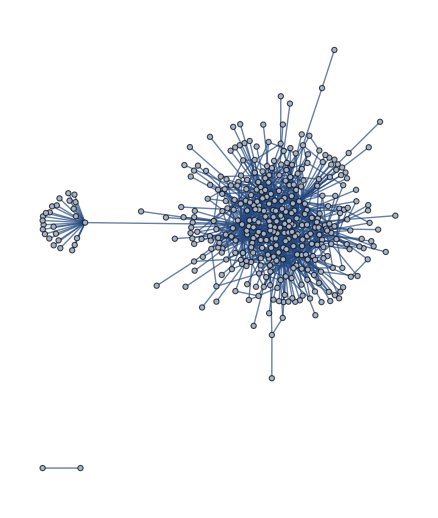

```mathematica
SocialMediaData["Facebook","BimodalLikeCommentNetwork","FormattedData"]
```

Contiguous US

-Graphics-

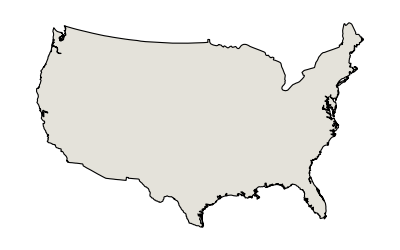

```mathematica
GraphData["ContiguousUSAGraph"]
CountryData["UnitedStates","Shape"]
```